Приложение В.

```mathematica
Needs["Splines`"];
```

```mathematica
(*Введеём начальные значения, по которым будем строить сплайн*)
```

```mathematica
n=3;
```

```mathematica
Uzl={0.1,0.3,0.7,1.4};
```

```mathematica
Znach={1,-7,15,25};
```

```mathematica
dF={-7,10,22,7};
```

```mathematica
Do[{Subscript[x, i]=Uzl⟦i+1⟧,Subscript[f, i]=Znach⟦i+1⟧,Subscript[df, i]=dF⟦i+1⟧},{i,0,n}]
```

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]},
PlotRange->{{0,1.5},{-40,40}}];
```

```mathematica
(*Построим сплайн Эрмита - Subscript[S, 3,2](x)*)
```

```mathematica
Do[Subscript[t, i][X_]=(X-Subscript[x, i])/(Subscript[x, i+1]-Subscript[x, i]),{i,0,n-1}];
```

```mathematica
Do[{Subscript[A, k]=-2(Subscript[f, k+1]-Subscript[f, k])/(Subscript[x, k+1]-Subscript[x, k])+(Subscript[df, k]+Subscript[df, k+1]),Subscript[B, k]=-Subscript[A, k]+(Subscript[f, k+1]-Subscript[f, k])/(Subscript[x, k+1]-Subscript[x, k])-Subscript[df, k]},
{k,0,n-1}];
```

```mathematica
Subscript[P, k_][X_]:=Subscript[f, k]+(X-Subscript[x, k])(Subscript[df, k]+Subscript[t, k][X](Subscript[B, k]+Subscript[t, k][X] Subscript[A, k]));
```

```mathematica
P[X_]=Table[Subscript[P, k][X],{k,0,n-1}]//Expand
```

{-6.175+171.25 X-1202.5 X^2+2075. X^3,30.8375-306.125 X+746.25 X^2-487.5 X^3,-6.4+39.5714 X-13.4694 X^2+0.874636 X^3}

```mathematica
G32=Table[Plot[P[X][[k]],{X,Subscript[x, k-1],Subscript[x, k]},PlotStyle->PointSize[0.05],
PlotRange->{{0,3},{-45,30}}],{k,1,n}];
```

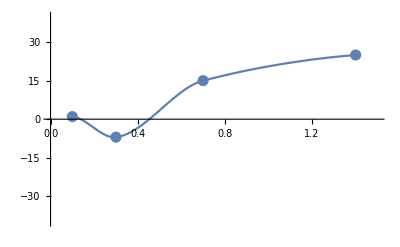

```mathematica
Show[Gr1,G32]
```

```mathematica
(*Проверим построенный сплайн втроенной функцией Spline(показана красной штриховкой)*)
```

```mathematica
Points={{0.1,1},{0.3,-7},{0.7,15},{1.4,25}};
```

```mathematica
GrH1=Graphics[{Red,Dashed,Spline[Points,Cubic]}];
```

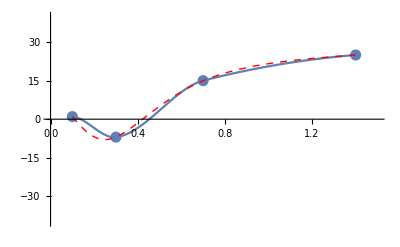

```mathematica
Show[Gr1,G32,GrH1]
```